# Investigate convolving with -2nd deriv for peak finding

## Set up the basic functions

f is the Lorentzian function/Cauchy PDF as defined in Paul Anderson's thesis.  This makes γ the width at half-height, amp the amplitude of the mode, and x0 the location of the mode on the x axis.

```mathematica
f[x_,amp_,γ_,x0_]:=amp γ^2/(4(x-x0)^2+γ^2)
```

d is the negative of the 2nd derivative of a unit height Lorentzian with unit width at half-height with its maximum at 0

```mathematica
d[x_]:=Evaluate[-D[f[x,1,1,0],{x,2}]]
```

Here you can see the formulas for d and the unit f

```mathematica
f[x,1,1,0]
```

1/(1+4 x^2)

```mathematica
d[x]
```

-(128 x^2)/((1+4 x^2)^3)+8/((1+4 x^2)^2)

And here they are, plotted together on the same graph

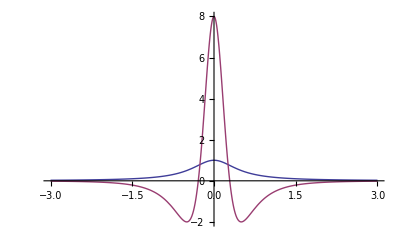

```mathematica
Plot[{f[x,1,1,0],d[x]},{x,-3,3},PlotRange->All]
```

## Is the -2nd derivative a zero-area filter?

Over the whole area, it is zero-area when parameterized acording to the normal parameterization

```mathematica
Integrate[d[x/2], {x, -Infinity, Infinity}]
```

0

However, when parameterized as Paul does, it comes up with a positive area

```mathematica
Integrate[d[x], {x, -Infinity, Infinity}]
```

(3 π)/4

I think this is a bug in the integration routine and that the area is zero no matter how we scale the x axis.

### Bug explanation

The indefinite integral of d is the first derivative of f.

```mathematica
dd[x_]:=Evaluate[-D[f[x,1,1,0],{x,1}]]
```

```mathematica
dd[x]
```

(8 x)/((1+4 x^2)^2)

We can look at this multiplied by q

```mathematica
dd[q x]
```

(8 q x)/((1+4 q^2 x^2)^2)

We can use the definition of improper integration to calculate the integral ∫_(-∞)^∞ fⅆx=∫_(-∞)^a fⅆx+∫_a^∞ fⅆx for some real a

And ∫_a^∞ fⅆx= lim_(t→∞) ∫_a^t fⅆx=lim_(t→∞) (F(t)-F(a))

I choose a=1 below.  Note that these results make perfect sense since lim_(x→∞) (8 q x)/((1+4 q^2 x^2)^2)=0 for both +∞ and -∞.  So ∫_(-∞)^a fⅆx+∫_a^∞ fⅆx=lim_(t→∞) (F(t)-F(a))+lim_(t→∞) (F(a)-F(t))=-F(a)+F(a)=0

We can check my calculations:

```mathematica
Limit[dd[q x]-dd[q],x->Infinity]
```

-(8 q)/((1+4 q^2)^2)

```mathematica
Limit[dd[q]-dd[q x],x->-Infinity]
```

(8 q)/((1+4 q^2)^2)

### Back to work

We can also motivate that the area is in general 0, by taking the limits of the truncated area in a symmetric region around the center as that region gets wider.

```mathematica
truncArea[w_]:=Integrate[d[x],{x,-w,w}]
```

```mathematica
truncArea[5]
```

80/10201

```mathematica
truncArea[100]
```

1600/1600080001

```mathematica
Limit[truncArea[x],x->Infinity]
```

0

In our work we will likely use a truncated version of the function and convolve it with our signal to find peaks.  As you can see above, the truncated version does not have 0 area.

What the people in the Hough transform paper did is to scale the positive section of the filter by a correction factor to make its area equal to that of the negative section.

The below shows that there is only one positive portion of the filter (and its boundaries)

```mathematica
Reduce[d[x]>0,{x}]
```

-1/(2 √3)<x<1/(2 √3)

The correcton factor is -negArea/posArea. Since there is only one positive portion of the graph, and it is a contiguous region centered on the origin.  Since the total_area = neg_area+pos_area.  One can calculate the negative area as totalArea-posArea.  Thus, -negArea/posArea=-(totalArea-posArea)/posArea=1-totalArea/posArea

So, the corrected truncated function for a width of 2.75 is:

```mathematica
trunc[x_]:=With[{w=1376/1000},With[{cf=1-(truncArea[w]/truncArea[1/(2 √3)])},If[Abs[x]<w,If[Abs[x]<1/(2 √3),cf d[x], d[x]],0]]]
```

A note about why I chose this width.  Below, I calculate that when peaks are separated by more than about 2.75, there is a spurious third peak.  I'm hoping that by truncating here, I may get rid of that third peak.

```mathematica
Integrate[trunc[x],{x,-3,3}]
```

0

## How does this filter work as a peak-detector?

### Performance for one function and the un-truncated filter

Here, we try convolve our filter with a single peak located at x0,  the result of this convolution is in oneFunction

```mathematica
oneFunction[y_,x0_]:=Evaluate[Assuming[Im[x0]==0,Convolve[f[x,1,1,x0],d[x],x,y]]]
```

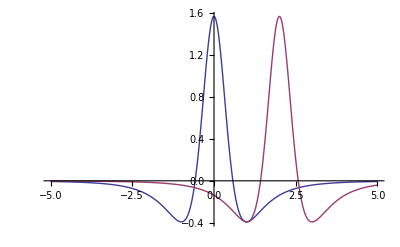

```mathematica
Plot[{oneFunction[x,0],oneFunction[x,2]},{x,-5,5},PlotRange->All]
```

This always has its maximum at x0.

```mathematica
Module[{q},q[x_]:=oneFunction[x,x0];Reduce[D[q[x],x]==0&&D[q[x],{x,2}]<0,Reals]]
```

x==x0

### Performance for two functions and the un-truncated filter

twoFunctions defines the convolution of our filter and two identical peaks.  One peak is at -x0 and the other at x0.  So the distance between them is 2 x0.

```mathematica
twoFunctions[y_,x0_]:=Evaluate[Assuming[Im[x0]==0,Convolve[f[x,1,1,-x0]+f[x,1,1,x0],d[x],x,y]]]
```

Both locations are maxima only when x0 ==0 or |x0|==1/2

```mathematica
Module[{q},q[x_]:=twoFunctions[x,x0];
With[{firstD=D[twoFunctions[x,x0],x],secD=D[twoFunctions[x,x0],{x,2}]},
With[{firstDAtNegX0=firstD/.x->-x0,firstDAtX0=firstD/.x->x0,
secDAtNegX0=secD/.x->-x0,secDAtX0=secD/.x->x0},
Reduce[firstDAtNegX0==0&&firstDAtX0==0&&secDAtNegX0<0&&secDAtX0<0,Reals]
]]]
```

x0==-1/2||x0==0||x0==1/2

These two conditions can be seen in the following plot (I left out the plot for x0==-1 for clarity)

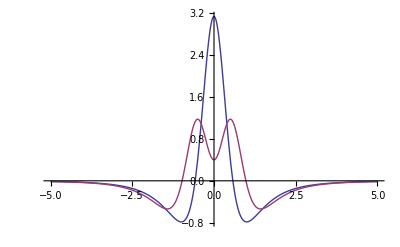

```mathematica
Plot[{twoFunctions[x,0],twoFunctions[x,1/2]},{x,-5,5},PlotRange->All]
```

Due to symmetry of the original and filter functions, the maxima must be located symmetrically.  Now, where are the positive maxima?

```mathematica
Module[{q},q[x_]:=twoFunctions[x,x0];
With[{firstD=D[twoFunctions[x,x0],x],secD=D[twoFunctions[x,x0],{x,2}]},
Reduce[firstD==0&&secD<0&&x0>=0&&x>=0,Reals]
]]
```

(0≤x0<Root[1-10 #1^2+5 #1^4&,3]&&x==0)||(Root[1-10 #1^2+5 #1^4&,3]<x0<Root[1-10 #1^2+5 #1^4&,4]&&x==Root[-1+7 x0^2+22 x0^4+14 x0^6-5 x0^8-5 x0^10+(-3-20 x0^2+38 x0^4+60 x0^6+5 x0^8) #1^2+(-2-54 x0^2-38 x0^4+14 x0^6) #1^4+(2-20 x0^2-22 x0^4) #1^6+(3+7 x0^2) #1^8+#1^10&,3])||(x0==Root[1-10 #1^2+5 #1^4&,4]&&x==Root[-1+7 x0^2+22 x0^4+14 x0^6-5 x0^8-5 x0^10+(-3-20 x0^2+38 x0^4+60 x0^6+5 x0^8) #1^2+(-2-54 x0^2-38 x0^4+14 x0^6) #1^4+(2-20 x0^2-22 x0^4) #1^6+(3+7 x0^2) #1^8+#1^10&,5])||(x0>Root[1-10 #1^2+5 #1^4&,4]&&(x==0||x==Root[-1+7 x0^2+22 x0^4+14 x0^6-5 x0^8-5 x0^10+(-3-20 x0^2+38 x0^4+60 x0^6+5 x0^8) #1^2+(-2-54 x0^2-38 x0^4+14 x0^6) #1^4+(2-20 x0^2-22 x0^4) #1^6+(3+7 x0^2) #1^8+#1^10&,5]))

When we look at this, result, we see that when x0 is large enough (greater than 1.38, that is when the peaks are separated by more than 2.75), there are 3 maxima!

```mathematica
N[Root[1-10 #1^2+5 #1^4&,4]]
```

1.37638

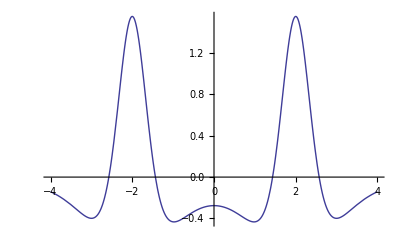

```mathematica
Plot[twoFunctions[x,2],{x,-4,4}]
```

When x0 is less than about 0.32492 then there is only one root.  That is, the peaks are indistinguishable when separated by 0.649839 units.

```mathematica
{N[Root[1-10 #1^2+5 #1^4&,3]],2*N[Root[1-10 #1^2+5 #1^4&,3]]}
```

{0.32492,0.649839}

That is not the end of the bad news.  Even if we can disregard the spurious detection at 0, we still get error in peak position.

twoFuncX gives the x position of the largest maximum for a given x0

```mathematica
twoFuncX[x0_]:=Which[
0≤Abs[x0]<Root[1-10 #1^2+5 #1^4&,3],0,
Root[1-10 #1^2+5 #1^4&,3]<Abs[x0]<Root[1-10 #1^2+5 #1^4&,4],Root[-1+7 x0^2+22 x0^4+14 x0^6-5 x0^8-5 x0^10+(-3-20 x0^2+38 x0^4+60 x0^6+5 x0^8) #1^2+(-2-54 x0^2-38 x0^4+14 x0^6) #1^4+(2-20 x0^2-22 x0^4) #1^6+(3+7 x0^2) #1^8+#1^10&,3],
Abs[x0]==Root[1-10 #1^2+5 #1^4&,4],Root[-1+7 x0^2+22 x0^4+14 x0^6-5 x0^8-5 x0^10+(-3-20 x0^2+38 x0^4+60 x0^6+5 x0^8) #1^2+(-2-54 x0^2-38 x0^4+14 x0^6) #1^4+(2-20 x0^2-22 x0^4) #1^6+(3+7 x0^2) #1^8+#1^10&,5],
x0>Root[1-10 #1^2+5 #1^4&,4],Root[-1+7 x0^2+22 x0^4+14 x0^6-5 x0^8-5 x0^10+(-3-20 x0^2+38 x0^4+60 x0^6+5 x0^8) #1^2+(-2-54 x0^2-38 x0^4+14 x0^6) #1^4+(2-20 x0^2-22 x0^4) #1^6+(3+7 x0^2) #1^8+#1^10&,5]
]
```

The error function grows seadily until the located maximum finally splits into two.  Then it decreases greatly, eventually overshooting.

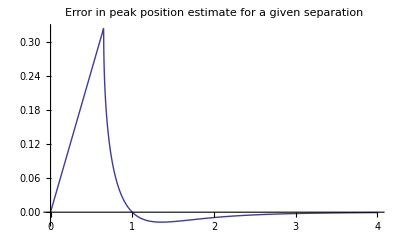

```mathematica
Plot[sep/2-twoFuncX[sep/2],{sep,0,4},PlotRange->All,PlotLabel->"Error in peak position estimate for a given separation",FrameLabel->{"Peak separation","Distance of predicted from actual peak"},AxesOrigin->{0,0}]
```

When expressed as a percentage of the distance of the peak from the center, the error looks better when they are separated by two peak widths (one unit).

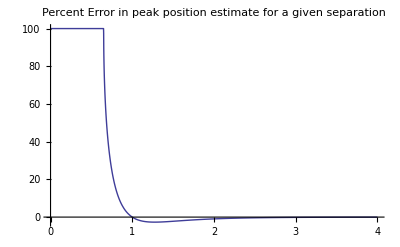

```mathematica
Plot[100*(sep/2-twoFuncX[sep/2])/(sep/2),{sep,0,4},PlotRange->All,PlotLabel->"Percent Error\nin peak position estimate for a given separation",FrameLabel->{"Peak separation","Distance of predicted from actual peak"},AxesOrigin->{0,0}]
```

The maximum % error when they are separated by more than 1 unit is: 2.67588% when they are separated by 1.27 units.

```mathematica
NMaximize[{Abs[(sep/2-twoFuncX[sep/2])/(sep/2)],sep>1},{sep}]
```

{0.0267588,{sep→1.27415}}

### Two functions and truncated filter

twoFunctions defines the convolution of our filter and two identical peaks.  One peak is at -x0 and the other at x0.  So the distance between them is 2 x0.

```mathematica
twoFunctionsTrunc[y_,x0_]:=Evaluate[Assuming[Im[x0]==0,Convolve[f[x,1,1,-x0]+f[x,1,1,x0],trunc[x],x,y]]]
```

Plotting the truncated version, it is clear that the truncation does not avoid the spurious central maximum.

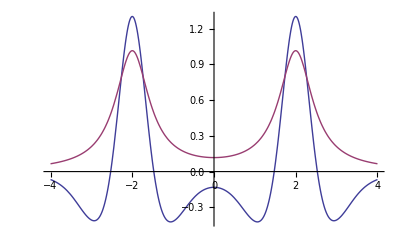

```mathematica
Plot[{twoFunctionsTrunc[x,2],f[x,1,1,-2]+f[x,1,1,2]},{x,-4,4},PlotRange->All]
```

### Other experiments

```mathematica
h[y_]:=Evaluate[Convolve[f[x,1,1,0]+f[x+2,1,1,0],trunc[x],x,y]]
```

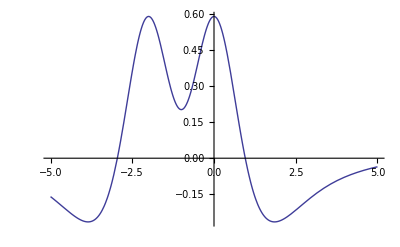

```mathematica
Plot[h[x],{x,-5,5},PlotRange->All]
```